Tisserand Curves

Plots

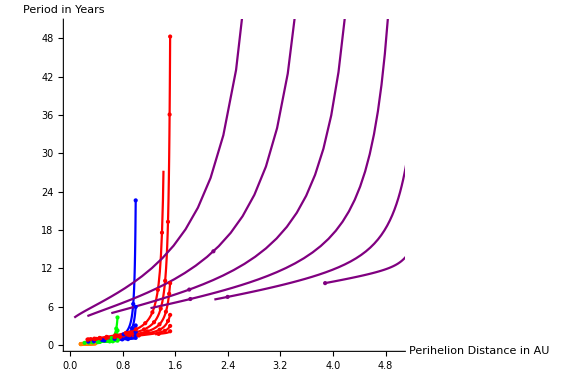

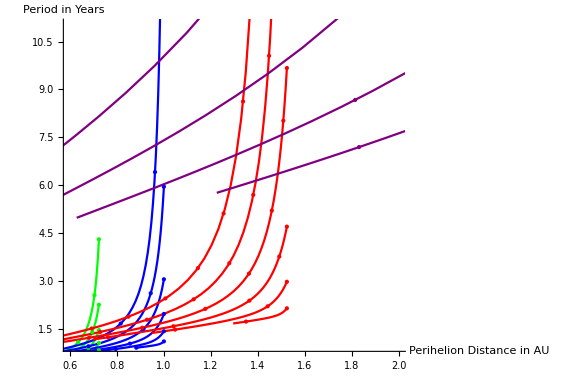

Trajectory Generation

Here are the Trajectories you can take from Earth

{3,3,2.87661,2,5,1.12549}

{3,5,2.08654,2,5,0.989074}

{3,5,2.24209,2,7,1.30231}

{3,5,2.48775,2,9,1.49633}

{3,7,1.83409,2,5,0.756049}

{3,7,1.93079,2,7,1.16748}

{3,7,2.06571,2,9,1.39658}

{3,7,2.25017,2,11,1.56389}

{3,9,1.75033,2,7,0.973895}

{3,9,1.84833,2,9,1.26059}

{3,9,1.97498,2,11,1.4557}

{3,11,1.61933,2,7,0.685515}

{3,11,1.69772,2,9,1.08133}

{3,11,1.79689,2,11,1.31837}

{3,5,0.926315,4,5,2.11997}

{3,5,0.687476,4,7,1.8673}

{3,7,1.25957,4,5,2.25869}

{3,7,1.12727,4,7,1.95287}

{3,7,0.936012,4,9,1.77863}

{3,7,0.647086,4,11,1.65416}

{3,9,1.45985,4,5,2.47427}

{3,9,1.36299,4,7,2.0719}

{3,9,1.2305,4,9,1.86501}

{3,9,1.05516,4,11,1.7231}

{3,11,1.61057,4,5,2.91174}

{3,11,1.53234,4,7,2.23297}

{3,11,1.42758,4,9,1.97638}

{3,11,1.2942,4,11,1.81035}

{3,11,0.714906,5,7,2.53138}

{3,11,0.629226,5,9,2.24578}

{3,11,0.505064,5,11,2.09261}

Number of created trajectories: 1148

Getting Time Metrics

Phasing Time

{0,185 °,101 °,174 °,163 °}

{0.0542226,0.0107603,0.,-0.00805573,-0.0157528}

142

850

254

321

Trajectory 142 should launch on Thu 21 Oct 2021 07:39:32

The phasing error is 0.456104 radians, or 26.1328 degrees

The Planets trajectory looks like this: {Earth,Venus,Mars,Earth,Jupiter}

The complete trajectory looks like this {3,5,2.48775,2,9,1.49633,0.708588,4,11,1.96847,1.81035,3,11,1.2942,0.714906,5,7,2.53138}

The time it takes to complete this trajectory is 1656.88 days

This is 4.53939 years

This means you arrive to the jupiter system on Tue 5 May 2026 04:42:51

This trajectory requires 4.30782 km/s of delta V to begin the unpowered flyby

This trajectory requires 8.21031 km/s of delta V to be captured in a circular orbit about Jupiter that is 5x the radius of Jupiter

This implies the minimum delta V requried for this mission is 12.5181 km/s

Trajectory 850 should launch on Sat 19 Nov 2044 11:01:49

The phasing error is 0.464598 radians, or 26.6195 degrees

The Planets trajectory looks like this: {Earth,Mars,Earth,Jupiter}

The complete trajectory looks like this {3,7,0.647086,4,11,1.65416,1.81035,3,11,1.2942,0.714906,5,7,2.53138}

The time it takes to complete this trajectory is 992.356 days

This is 2.71878 years

This means you arrive to the jupiter system on Thu 8 Aug 2047 19:34:07

This trajectory requires 5.26222 km/s of delta V to begin the unpowered flyby

This trajectory requires 8.21031 km/s of delta V to be captured in a circular orbit about Jupiter that is 5x the radius of Jupiter

This implies the minimum delta V requried for this mission is 13.4725 km/s

Trajectory 254 should launch on Wed 29 Jul 2037 10:16:28

The phasing error is 0.0221297 radians, or 1.26794 degrees

The Planets trajectory looks like this: {Earth,Venus,Earth,Earth,Jupiter}

The complete trajectory looks like this {3,7,2.06571,2,9,1.39658,1.08133,3,11,1.69772,1.69772,3,11,1.0168,0.629226,5,9,2.24578}

The time it takes to complete this trajectory is 1427.01 days

This is 3.90963 years

This means you arrive to the jupiter system on Tue 25 Jun 2041 10:36:11

This trajectory requires 5.26222 km/s of delta V to begin the unpowered flyby

This trajectory requires 8.82587 km/s of delta V to be captured in a circular orbit about Jupiter that is 5x the radius of Jupiter

This implies the minimum delta V requried for this mission is 14.0881 km/s

Trajectory 321 should launch on Fri 27 Jan 2017 15:38:26

The phasing error is 0.703498 radians, or 40.3075 degrees

The Planets trajectory looks like this: {Earth,Venus,Mars,Mars,Earth,Jupiter}

The complete trajectory looks like this {3,7,2.25017,2,11,1.56389,0.995509,4,11,2.00854,2.00854,4,11,1.82857,1.81035,3,11,1.2942,0.629226,5,9,2.24578}

The time it takes to complete this trajectory is 1503.79 days

This is 4.11996 years

This means you arrive to the jupiter system on Thu 11 Mar 2021 10:30:45

This trajectory requires 5.26222 km/s of delta V to begin the unpowered flyby

This trajectory requires 8.82587 km/s of delta V to be captured in a circular orbit about Jupiter that is 5x the radius of Jupiter

This implies the minimum delta V requried for this mission is 14.0881 km/s

```mathematica
G=6.6742/10^20; (*Universal Gravity Constant[km3/kg/s2]*)
AU=149597887; (*Astronomical Unit[km]*)
MSun =1.988435`7.*^30;(*Solar Mass[kg]*)
μSun = MSun * G;(*Gravitational constant of the Sun[km3/s2]*)
Year = 2*Pi*Sqrt[AU^3/μSun];(*seconds*)
Day = 24*60*60;(*seconds*)
muSunDayAU = μSun*Day^2/AU^3;
Specific Data about Mercury;
MMercury=3.301039*10^23;
μMercury=MMercury*G;
distMercury=5.7909175*^7;
AltLimMercury=200;
RMercury=2.4397`5.*^3;
vMercury=Sqrt[μSun/distMercury];
ωMercury=vMercury/distMercury;

Specific Data about Venus;
MVenus =  4.869`5.*^24; (*Mass of the planet[kg]*)
μVenus = MVenus*G;(*Gravitational constant of the planet[km3/s2]*)
distVenus =108208926; (*Distance between the Sun and the palnet[km]*)
AltLimVenus=200;(*Altitude limit from the planet's surface during flyby[km]*)
RVenus = 6051.9; (*Radius of the planet[km]*)
vVenus = Sqrt[μSun/distVenus];(*Planet velocity around the Sun[km/s]*)
ωVenus=vVenus/distVenus;(*Planet angular velocity around the Sun[rad/s]*)
Specific Data about Earth;
MEarth= 5.9721986*^24;
μEarth= MEarth*G;
distEarth=AU;
AltLimEarth=200;
REarth= 6371.0087714;
vEarth= Sqrt[μSun/distEarth];
ωEarth=vEarth/distEarth;
Specific Data about Mars;
MMars=6.4191000000000000000007`5.*^23;
μMars= MMars*G;
distMars=227936637;
AltLimMars=200;
RMars= 3.386`4.*^3;
vMars = Sqrt[μSun/distMars];
ωMars=vMars/distMars;
Specific Data about Jupiter;
MJupiter= 1.8988`5.*^27;
μJupiter= MJupiter*G;
distJupiter=778412026;
RJupiter= 6.9173`5.*^4;
AltLimJupiter=5*RJupiter;
vJupiter= Sqrt[μSun/distJupiter];
ωJupiter=vJupiter/distJupiter;
Specific Data about Saturn;
MSaturn=5.68319*^26;
μSaturn=MSaturn*G;
distSaturn=1.426725*^9;
RSaturn=5.7316`5.*^4;
AltLimSaturn=2*RSaturn; (*So you dont hit rings*)
vSaturn=Sqrt[μSun/distSaturn];
ωSaturn=vSaturn/distSaturn;
(*collect*)
Rp={distMercury,distVenus,distEarth,distMars,distJupiter,distSaturn};
Vp={vMercury,vVenus,vEarth,vMars,vJupiter,vSaturn};
Radius={RMercury,RVenus,REarth,RMars,RJupiter,RSaturn};
Mplan={MMercury,MVenus,MEarth,MMars,MJupiter,MSaturn};
μ={μMercury,μVenus,μEarth,μMars,μJupiter,μSaturn};
μPlan=G*Mplan;
rplanet1={AltLimMercury+RMercury,AltLimVenus+RVenus,AltLimEarth+REarth,AltLimMars+RMars,AltLimJupiter+RJupiter,AltLimSaturn+RSaturn};
closestApproach = {AltLimMercury,AltLimVenus,AltLimEarth,AltLimMars,AltLimJupiter};
μSun=1.3271212876999998*^11;
(*km3/s2*)
vInfVals = {1,3,5,7,9,11};(*km/s*)
planetColors = {Orange,Green,Blue,Red,Purple,Black};
planetNames = {"Mercury","Venus","Earth","Mars","Jupiter"};

Print["Tisserand Curves"];
TisserandCurve[Vinf_,planetNumber_,alpha_] := 
Module[{planetSunDistance,velocityPlanet,vTotal,semimajoraxis,rVector,eccentricityVector,perihelionDistance,Time},
planetSunDistance = Rp[[planetNumber]];
velocityPlanet = Vp[[planetNumber]];
vTotal = {velocityPlanet + Vinf*Cos[alpha],Vinf*Sin[alpha],0};
semimajoraxis[alpha] = μSun*planetSunDistance/(2*μSun - planetSunDistance*(vTotal.vTotal));
rVector = {0,planetSunDistance,0};
eccentricityVector[alpha] = Cross[vTotal,Cross[rVector,vTotal]]/μSun - rVector/planetSunDistance;
perihelionDistance[alpha] =  semimajoraxis[alpha] * (1- Norm[eccentricityVector[alpha]])/AU;
Time[alpha] = 2*Pi* Sqrt[semimajoraxis[alpha]^3 / μSun]/Year;
{perihelionDistance[alpha],Time[alpha]}];
deltaAlpha[Vinf_,planetNumber_] := 2*ArcSin[1./(1 +( Radius[[planetNumber]]+ closestApproach[[planetNumber]])*
Vinf^2/μ[[planetNumber]])];
getOnePlanetPlot[Vinf_,planetNumber_] := ListPlot[
Table[Evaluate[TisserandCurve[Vinf,planetNumber, alpha]],{alpha,0,Pi,deltaAlpha[Vinf,planetNumber]}],
PlotStyle->{planetColors[[planetNumber]],PointSize[Medium]}];
getAllPlanetsPlots = Table[Table[getOnePlanetPlot[Vinf, planetNumber],{Vinf, vInfVals}],{planetNumber,{1,2,3,4,5}}];
plot1 = Table[
Table[
ListPlot[
Evaluate[
Table[
TisserandCurve[Vinf,planetNumber,alpha],{alpha,0,Pi,0.05}]],
Joined->True,PlotStyle->planetColors[[planetNumber]] ],
{Vinf,vInfVals}],{planetNumber,{1,2,3,4,5}}];

Print["Plots"];
Show[{plot1,getAllPlanetsPlots},PlotRange-> {{0,5},{0,50}},AspectRatio-> 2/3,
AxesLabel-> {"Perihelion Distance in AU","Period in Years"},
AxesOrigin-> Automatic,
ImageSize-> Large]
Show[{plot1,getAllPlanetsPlots},PlotRange-> {{0.6,2},{1,11}},AspectRatio-> 2/3,
AxesLabel-> {"Perihelion Distance in AU","Period in Years"},
AxesOrigin-> Automatic,
ImageSize-> Large]


earth[Vinf_,alpha_] := TisserandCurve[Vinf,3,alpha];
venus[Vinf_,alpha_] := TisserandCurve[Vinf,2,alpha];
mars[Vinf_,alpha_] := TisserandCurve[Vinf,4,alpha];
jupiter[Vinf_,alpha_] := TisserandCurve[Vinf,5,alpha];
mercury[Vinf_,alpha_]:= TisserandCurve[Vinf,1,alpha];
planetTisserands = {mercury,venus,earth,mars,jupiter};


Print["Trajectory Generation"];
(*Note: For find root we need to supply a initial guess - because of this, i recognize that earth will tend to hit venus on higher values of alpha,
Mars will collide on lower values of alpha,
Jupiter collides on lower values of alpha
This will help us shorten our zone to make find root go faster
Also Will hard code some information to make the search smarter*)
(*Forward Curves*)
venus3Earth = {3};
venus5Earth = {3,5,7,9};
(*venus6Earth = {5,6,7,9,11};*)
venus7Earth = {5,7,9,11};
venus9Earth = {5,7,9,11};
venus11Earth = {7,9,11};
venusEarthGuess = {1,2};

earth5Mars = {5,7};
(*earth6Mars = {5,6,7,9};*)
earth7Mars = {5,7,9,11};
earth9Mars = {5,7,9,11};
earth11Mars = {5,7,9,11};
earthMarsGuess = {0.3,2};

(*venus6Mars = {5,6};*)
venus7Mars = {5,7,9};
venus9Mars={7,9,11};
venus11Mars={7,9,11};
venusMarsGuess = {0.5,2};

(*Direct JUPITER OPTIONS*)
earth9Jupiter = {};
earth11Jupiter = {7,9,11};
earthJupiterGuess = {0.1,2.5};

mars7Jupiter = {5,7};
mars9Jupiter = {5,7,9,11};
mars11Jupiter = {5,7,9,11};
marsJupiterGuess = {1,3};

(*Backwards Curves*)
earth3Venus = {5};(*This should be read as: The earth 3 km/s Vinf curve intersects venus's 5km/s curve and thats it*)
earth5Venus = {5,7,9};
(*earth6Venus = {5,6,7,9,11};*)
earth7Venus = {5,7,9,11};
earth9Venus = {7,9,11};
earth11Venus = {7,9,11};
earthVenusGuess = {2,1};

mars5Earth = {5,7,9,11};
(*mars6Earth = {5,6,7,9,11};*)
mars7Earth = {5,7,9,11};
mars9Earth ={7,9,11};
mars11Earth = {7,9,11};
marsEarthGuess = {2,0.3};

(*Would never use these trajectories*)
mars5Venus = {7};
(*mars6Venus = {6,7,9,11};*)
mars7Venus = {7,9,11};
mars9Venus = {7,9,11};
mars11Venus = {9,11};

jupiter5Mars = {7,9,11};
(*jupiter6Mars = {7,9,11};*)
jupiter7Mars = {7,9,11};
jupiter9Mars = {9,11};
jupiter11Mars = {9,11};

(*jupiter6Earth = {9,11};*)
jupiter7Earth = {11};
jupiter9Earth = {11};
jupiter11Earth = {11};

allOptionsList = {
{{},{},{},{},{}},

{{},{},{venus3Earth,venus5Earth,venus7Earth,venus9Earth,venus11Earth,venusEarthGuess},{{},{},venus7Mars,venus9Mars,venus11Mars,venusMarsGuess},{}},

{{},{earth3Venus,earth5Venus,earth7Venus,earth9Venus,earth11Venus,earthVenusGuess},{},{{},earth5Mars,earth7Mars,earth9Mars,earth11Mars,earthMarsGuess},{{},{},{},earth9Jupiter,earth11Jupiter,earthJupiterGuess}},

{{},{},{{},mars5Earth,mars7Earth,mars9Earth,mars11Earth,marsEarthGuess},{},{{},{},mars7Jupiter,mars9Jupiter,mars11Jupiter,marsJupiterGuess}}
};
checkGeneral[planet1Vinf_,planet1VinFlist_,planet1Number_,planet2Number_,planet1Guess_,planet2Guess_] := Module[
{answerList,planet1Alpha,planet2Alpha,planet2Vinf,solution},
answerList = {};
For[z=1,z ≤Length[planet1VinFlist],z++,
Clear[planet1Alpha,planet2Alpha,earthAlpha,venusAlpha,solution];
planet2Vinf = planet1VinFlist[[z]];
solution = FindRoot[planetTisserands[[planet1Number]][planet1Vinf,planet1Alpha] - planetTisserands[[planet2Number]][planet2Vinf,planet2Alpha],{{planet1Alpha,planet1Guess,0,Pi},{planet2Alpha,planet2Guess,0,Pi}}];
AppendTo[answerList,{planet1Number,planet2Number,planet1Vinf,planet2Vinf,planet1Alpha/.solution,planet2Alpha/.solution}]
];
{answerList}]

formatGeneralSolutions[listOfOptions_] := Module[
{iterableOptions,formatedTrajectory,allTrajectoriesFormated},
iterableOptions = listOfOptions[[1]];
allTrajectoriesFormated = {};
For[x=1,x≤ Length[iterableOptions],x++,
trajectory = iterableOptions[[x]];

departPlanetNum = trajectory[[1]];
departPlanetVinf = trajectory[[3]];
departPlanetAlpha = trajectory[[5]];
arrivePlanetNum = trajectory[[2]];
arrivePlanetVinf = trajectory[[4]];
arrivePlanetAlpha = trajectory[[6]];
formatedTrajectory = {departPlanetNum,departPlanetVinf,departPlanetAlpha,arrivePlanetNum,arrivePlanetVinf,arrivePlanetAlpha};
AppendTo[allTrajectoriesFormated,formatedTrajectory];
];
{allTrajectoriesFormated}
]

Clear[trajectories,allTrajectories,earthConnectingOptions,earthVinf,earthAlphaGuess,nextPlanetAlphaGuess,sol,planet1Number,planet2Number,
planet1Vinf,planet1VinFlist,planetOptions,i,j,x,z];
getEarthStartingTrajectories[allOptionsList_] := Module[
{trajectories,allTrajectories,earthConnectingOptions,earthVinf,earthAlphaGuess,nextPlanetAlphaGuess,sol,planet1Number,planet2Number,
planet1Vinf,planet1VinFlist,planetOptions},

earthConnectingOptions = allOptionsList[[3]];
planet1Number = 3;
allTrajectories = {};

For[i=2,i≤Length[earthConnectingOptions],i++,
planetOptions = earthConnectingOptions[[i]];
If[planetOptions=={},
Nothing,
earthAlphaGuess = planetOptions[[-1]][[1]];
nextPlanetAlphaGuess = planetOptions[[-1]][[2]];
planet2Number = i;
For[j=1,j≤Length[planetOptions]-1,j++,
(*Print[planet1Vinf," ", planet1VinFlist," ",planet1Number," ",planet2Number," ",earthAlphaGuess," ",nextPlanetAlphaGuess];*)
planet1VinFlist = planetOptions[[j]];
If[planet1VinFlist == {},
Nothing,
planet1Vinf = vInfVals[[j+1]];
(*Print["Before Test: i = ", i, " ",planet1Vinf," ", planet1VinFlist];*)
sol = checkGeneral[planet1Vinf,planet1VinFlist,planet1Number,planet2Number,earthAlphaGuess,nextPlanetAlphaGuess];
(*Print["After Test: i = ",i, " ",planet1Vinf," ", planet1VinFlist];*)
trajectories = formatGeneralSolutions[sol][[1]];
(*Print[trajectories];*)
For[k=1,k≤Length[trajectories],k++,
AppendTo[allTrajectories,trajectories[[k]]]
];
]
];
];
];
{allTrajectories}
]

earthBoundTrajectories = getEarthStartingTrajectories[allOptionsList][[1]];
Print["Here are the Trajectories you can take from Earth"];

mappingFunction[planetVinf_] := Module[
{correctIndex},
If[planetVinf == 3,correctIndex = 1,
If[planetVinf == 5, correctIndex= 2,
If[planetVinf == 7, correctIndex= 3,
If[planetVinf == 9, correctIndex = 4,
If[planetVinf == 11, correctIndex= 5]]]]];
{correctIndex}]
reverseMappingFunction[correctIndexFromVInf_] := Module[
{correctVinf},
If[correctIndexFromVInf == 1,correctVinf = 3,
If[correctIndexFromVInf == 2, correctVinf= 5,
If[correctIndexFromVInf == 3, correctVinf=7,
If[correctIndexFromVInf == 4, correctVinf = 9,
If[correctIndexFromVInf == 5, correctVinf= 11]]]]];
{correctVinf}]

getChildTrajectories[startingTrajectory_,planet1VinfPlanet2list_,alphaGuessList_,nextPlanetNum_]:= Module[
{newTrajectory,newTrajectoryList,maxDeltaAlpha,actualDeltaAlpha,numFlybies,initialFlybyTrajectory},
newTrajectoryList = {};
solX = checkGeneral[startingTrajectory[[-2]],planet1VinfPlanet2list,startingTrajectory[[-3]],nextPlanetNum,alphaGuessList[[1]],alphaGuessList[[2]]][[1]];
For[w=1,w ≤ Length[solX],w++,
individualSol = solX[[w]];
(*Print[individualSol];*)
newTrajectory = startingTrajectory;
maxDeltaAlpha=deltaAlpha[startingTrajectory[[-2]],startingTrajectory[[-3]]];
(*Print[maxDeltaAlpha];
Print["You are at an alpha value of ",startingTrajectory[[-1]]];
Print["You need to be at an alpha value of ",individualSol[[5]]];*)
actualDeltaAlpha = Abs[individualSol[[5]] - startingTrajectory[[-1]]];
If[actualDeltaAlpha<maxDeltaAlpha,
AppendTo[newTrajectory,individualSol[[5]]];
AppendTo[newTrajectory,individualSol[[2]]];
AppendTo[newTrajectory,individualSol[[4]]];
AppendTo[newTrajectory,individualSol[[6]]];
AppendTo[newTrajectoryList,newTrajectory];
, 
numFlybies = Ceiling[actualDeltaAlpha/maxDeltaAlpha];
initialFlybyTrajectory = startingTrajectory;
For[y= 1,y ≤ numFlybies-1,y++,
AppendTo[newTrajectory,initialFlybyTrajectory[[-1]]];
AppendTo[newTrajectory,initialFlybyTrajectory[[-3]]];
AppendTo[newTrajectory,initialFlybyTrajectory[[-2]]];
AppendTo[newTrajectory,initialFlybyTrajectory[[-1]]-maxDeltaAlpha];
initialFlybyTrajectory = newTrajectory;
];
AppendTo[newTrajectory,individualSol[[5]]];
AppendTo[newTrajectory,individualSol[[2]]];
AppendTo[newTrajectory,individualSol[[4]]];
AppendTo[newTrajectory,individualSol[[6]]];
AppendTo[newTrajectoryList,newTrajectory];
];
];
(*Important Variable description: Each trajectory should be read in triplets
Each triplet corresponds to PlanetNumber, Vinf, alpha*)
{newTrajectoryList}]

Clear[sol,finalTrajectoryList,planet1,planet1Vinf,planet1Alpha,trajectory1,
availableVinfLists,currentPlanetToNextPlanetVinfAvailbleList,index,onlyAvailableVinfConnectionList,newTrajectory,lengthOfTrajectory,minimumVinf,planetVinfList,startingTrajectory,buildEntireTrajectory];
buildEntireTrajectory[startingTrajectory_] := Module[
{finalTrajectoryList,planet1,planet1Vinf,planet1Alpha,trajectory1,
availableVinfLists,currentPlanetToNextPlanetVinfAvailbleList,index,onlyAvailableVinfConnectionList,newTrajectory,lengthOfTrajectory,minimumVinf,planetVinfList},


planet1 = startingTrajectory[[-3]];
planet1Vinf = startingTrajectory[[-2]];
planet1Alpha = startingTrajectory[[-1]];
trajectory1 = startingTrajectory;
finalTrajectoryList = {};
lengthOfTrajectory = 2;



index = mappingFunction[planet1Vinf];

availableVinfLists = allOptionsList[[planet1]];
(*Print[trajectory1];*)
(*c represents the next Planet!*)
For[c=1,c≤Length[availableVinfLists],c++,

currentPlanetToNextPlanetVinfAvailbleList = availableVinfLists[[c]];

If[currentPlanetToNextPlanetVinfAvailbleList == {},
Nothing,

onlyAvailableVinfConnectionList = currentPlanetToNextPlanetVinfAvailbleList[[index]][[1]];

If[onlyAvailableVinfConnectionList=={},
Nothing,

alphaGuessList = currentPlanetToNextPlanetVinfAvailbleList[[-1]];
sol = getChildTrajectories[trajectory1,onlyAvailableVinfConnectionList,alphaGuessList,c][[1]];

For[q=1,q≤Length[sol],q++,
(*Print["Q: ",q];*)
(*Print[sol, " ", q];*)
newTrajectory = sol[[q]];
nextPlanet1 = newTrajectory[[-3]];
nextPlanet1Vinf = newTrajectory[[-2]];
nextPlanet1Alpha = newTrajectory[[-1]];
(*Print["Next Planet is ", nextPlanet1];*)
index1 = mappingFunction[nextPlanet1Vinf];
nextPlanet1AvailableVinfLists = allOptionsList[[nextPlanet1]];
If[nextPlanet1 == 5,
(*Print["We hit Jupiter"];*)
AppendTo[finalTrajectoryList,newTrajectory],
(*Print["Layer 1"];*)
For[c2=1,c2≤Length[nextPlanet1AvailableVinfLists],c2++,
planetAvailbleVinfLists = nextPlanet1AvailableVinfLists[[c2]];
(*Print["Look Here 1",planetAvailbleVinfLists];*)
If[planetAvailbleVinfLists == {},
Nothing,
onlyAvailableVinfConnectionList2 = planetAvailbleVinfLists[[index1]][[1]];
(*Print["Look Here 2",onlyAvailableVinfConnectionList2];*)
If[onlyAvailableVinfConnectionList2 == {},
Nothing,
alphaGuessList2 = planetAvailbleVinfLists[[-1]];
(*Print[newTrajectory," ",onlyAvailableVinfConnectionList2," ",alphaGuessList2," ",c2];*)
sol2 = getChildTrajectories[newTrajectory,onlyAvailableVinfConnectionList2,alphaGuessList2,c2][[1]];
(*Print["Generated Sols: ", sol2];*)

For[q2=1,q2≤Length[sol2],q2++,
newTrajectory2 = sol2[[q2]];
(*Print["Trajectory 2", newTrajectory2];*)
nextPlanet2 = newTrajectory2[[-3]];
nextPlanet2Vinf = newTrajectory2[[-2]];
nextPlanet2Alpha = newTrajectory2[[-1]];
index2 = mappingFunction[nextPlanet2Vinf];
nextPlanet2AvailableVinfLists = allOptionsList[[nextPlanet2]];
(*Print[newTrajectory];*)
If[nextPlanet2 == 5,
(*Print["We hit Jupiter"];*)
AppendTo[finalTrajectoryList,newTrajectory2],
(*Print["Layer 2"];*)
For[c3=1,c3≤Length[nextPlanet2AvailableVinfLists],c3++,
planetAvailbleVinfLists2 = nextPlanet2AvailableVinfLists[[c3]];
If[planetAvailbleVinfLists2 == {},
Nothing,
onlyAvailableVinfConnectionList3 = planetAvailbleVinfLists2[[index2]][[1]];
If[onlyAvailableVinfConnectionList3 == {},
Nothing,
alphaGuessList3 = planetAvailbleVinfLists2[[-1]];
(*Print[newTrajectory2," ",onlyAvailableVinfConnectionList3," ",alphaGuessList3," ",c3];*)
sol3= getChildTrajectories[newTrajectory2,onlyAvailableVinfConnectionList3,alphaGuessList3,c3][[1]];
(*Print["Generated sols: ", sol3];*)

For[q3=1,q3<=Length[sol3],q3++,
newTrajectory3 = sol3[[q3]];
(*Print["Trajectory 3", newTrajectory3];*)
nextPlanet3 = newTrajectory3[[-3]];
nextPlanet3Vinf = newTrajectory3[[-2]];
nextPlanet3Alpha = newTrajectory3[[-1]];
index3 = mappingFunction[nextPlanet3Vinf];
nextPlanet3AvailableVinfLists = allOptionsList[[nextPlanet3]];
(*Print[newTrajectory];*)
If[nextPlanet3 == 5,
(*Print["We hit Jupiter"];*)
AppendTo[finalTrajectoryList,newTrajectory3],
(*Print["Layer 3"];*)
For[c4=1,c4≤Length[nextPlanet3AvailableVinfLists],c4++,
planetAvailbleVinfLists3 = nextPlanet3AvailableVinfLists[[c4]];
(*Print["C4 " ,c4];*)
If[planetAvailbleVinfLists3 == {},
Nothing,
onlyAvailableVinfConnectionList4 = planetAvailbleVinfLists3[[index3]][[1]];
(*Print[onlyAvailableVinfConnectionList4];*)
If[onlyAvailableVinfConnectionList4 == {},
Nothing,
alphaGuessList4 = planetAvailbleVinfLists3[[-1]];
(*Print[newTrajectory3," ",onlyAvailableVinfConnectionList4," ",alphaGuessList4," ",c4];*)
sol4= getChildTrajectories[newTrajectory2,onlyAvailableVinfConnectionList3,alphaGuessList3,c3][[1]];
(*Print["Generated sols: ", sol4];*)
For[q4 = 1,q4≤ Length[sol4],q4++,
If[sol4[[q4]][[-3]] == 5, 
(*Print["Hit Jupiter"];*)
AppendTo[finalTrajectoryList,sol4[[q4]]],
Nothing]
]
]
]
]
]
]
]
]
]
]
]
]
]
]
]
]
]
]
];
{finalTrajectoryList}
]


createALLTRAJECTORIES[earthBoundTrajectories_] := Module[
{finalList,jupiterOptions},
finalList ={};
For[b=1,b≤ Length[earthBoundTrajectories],b++,
Print[earthBoundTrajectories[[b]]];
jupiterOptions = Quiet[buildEntireTrajectory[earthBoundTrajectories[[b]]]][[1]];
For[u=1,u≤ Length[jupiterOptions],u++,
AppendTo[finalList,jupiterOptions[[u]]]
]
];
{finalList}
]
allJupiterBoundTrajectories = createALLTRAJECTORIES[earthBoundTrajectories];
Print["Number of created trajectories: ", Length[allJupiterBoundTrajectories[[1]]]];


Clear[testCase,t,allTrajectories,trajectory,planetNum,vInfEachTraj,planetIndiciesEachTraj,aValsEachTraj,thetaForTrajectory];
(*Note that we need to define the list of Vinf for the trajectory, planet index, and alpha values*)
trajectoryFunction[transferNum_,initialTheta_, vInfEachTraj_,planetIndiciesEachTraj_,aValsEachTraj_] := 
Module[
{firstVinf,firstPlanet,nextPlanet,firstAlpha,
v1Sign,v1Next,v2Next,firstR0,nextPlanetRadius,reapOutput},
firstVinf = vInfEachTraj[[transferNum]];
firstPlanet = planetIndiciesEachTraj[[transferNum]];
nextPlanet = planetIndiciesEachTraj[[transferNum+1]];
(*Print["First Planet : ", firstPlanet, " Second Planet ", nextPlanet];*)
firstAlpha = aValsEachTraj[[transferNum]];
firstR0 = Rp[[firstPlanet]]/AU;
nextPlanetRadius = Rp[[nextPlanet]]/AU;
v1Sign = If[nextPlanetRadius ≠ firstR0, Sign[nextPlanetRadius - firstR0],1];
v1Next = v1Sign*Sin[firstAlpha]*firstVinf;
v2Next = Vp[[firstPlanet]] + Cos[firstAlpha]*firstVinf;
v1Next *= Day/AU;
v2Next *= Day/AU;
(*Print[firstR0," ", initialTheta, " " ,v1Next, " ", v2Next, " " ,v2Next/firstR0];*)
reapOutput = Reap[NDSolve[
{r''[t]-r[t]*theta'[t]^2==-muSunDayAU/r[t]^2,
r[t]*theta''[t]+2*r'[t]*theta'[t]==0,
r[0]==firstR0,theta[0]==initialTheta,r'[0]==v1Next,theta'[0]==v2Next/r[0],
WhenEvent[r[t] - nextPlanetRadius,
Sow[{t,theta[t] - initialTheta, (theta[t] - initialTheta)/Degree, Mod[theta[t],2*Pi],
Mod[theta[t],2*Pi]/Degree}]]},{r,theta}, {t,0,5000}]];
(*Print[reapOutput];*)
{reapOutput[[1]][[1]],{reapOutput[[2]][[1]][[1]],reapOutput[[2]][[1]][[2]]},
initialTheta}
];
Clear[testCase,t,allTrajectories,trajectory,planetNum,vInfEachTraj,planetIndiciesEachTraj,aValsEachTraj,thetaForTrajectory];
runTrajectoryAnalysis[allTrajectories_] := Module[
{trajectory,vInfEachTraj,planetIndiciesEachTraj,aValsEachTraj,thetaForTrajectory,informationList,performanceList,finalList},

finalList= {};

For[y=1,y≤Length[allTrajectories],y++,
informationList = {};
trajectory = allTrajectories[[y]];
(*Print[trajectory];*)
vInfEachTraj = {trajectory[[2]]};
planetIndiciesEachTraj = {trajectory[[1]]};
aValsEachTraj = {trajectory[[3]]};

For[vv=4,vv≤Length[trajectory],vv+=4,
planetNum = trajectory[[vv]];
vInf = trajectory[[vv+1]];
If[vv+2 == Length[trajectory],Nothing,
planetAlpha = trajectory[[vv+3]];
];
AppendTo[planetIndiciesEachTraj,planetNum];
AppendTo[vInfEachTraj,vInf];
AppendTo[aValsEachTraj,planetAlpha]
];
thetaForTrajectory = 0;
option1ListTime = {};
option1ListDeltaTheta = {};
option2ListTime = {};
option2ListDeltaTheta = {};
(*Print[planetIndiciesEachTraj, " ",vInfEachTraj," ", aValsEachTraj];*)
For[tn=1,tn≤Length[planetIndiciesEachTraj]-1,tn++,
(*Print["Transfer Number: ",tn];*)
trajectoryFunctionOutput = trajectoryFunction[tn,thetaForTrajectory,vInfEachTraj,planetIndiciesEachTraj,aValsEachTraj][[2]];

trajectoryOption1Information = trajectoryFunctionOutput[[1]];
trajectoryOption1TransferTime = trajectoryOption1Information[[1]];
trajectoryOption1DeltaThetaRadians = trajectoryOption1Information[[2]];
trajectoryOption1ThetaInstersect = trajectoryOption1Information[[3]];

AppendTo[option1ListTime,trajectoryOption1TransferTime];
AppendTo[option1ListDeltaTheta,trajectoryOption1DeltaThetaRadians];


trajectoryOption2Information = trajectoryFunctionOutput[[2]];
trajectoryOption2TransferTime = trajectoryOption2Information[[1]];
trajectoryOption2DeltaThetaRadians = trajectoryOption2Information[[2]];

AppendTo[option2ListTime,trajectoryOption2TransferTime];
AppendTo[option2ListDeltaTheta,trajectoryOption2DeltaThetaRadians];

(*Just use this once case, techincally there are more - need to think about this*)
thetaForTrajectory = trajectoryOption1ThetaInstersect;
];
(*Print[option1ListTime];
Print[option1ListDeltaTheta];
Print[option2ListTime];
Print[option2ListDeltaTheta];*)
informationList = {trajectory,{option1ListTime,option1ListDeltaTheta},{option2ListTime,option2ListDeltaTheta}};
AppendTo[finalList,informationList];
];
{finalList}
]
allTrajectoryInformation = runTrajectoryAnalysis[allJupiterBoundTrajectories[[1]]];

getImportantMetrics[trajectoryInformation_] := Module[
{trajTimeVelocity},
trajectory = trajectoryInformation[[1]];
initialDeltaV = trajectory[[2]];

option1Information = trajectoryInformation[[2]];
option1TimeInformationDays = option1Information[[1]];
option1TotalTime = Total[option1TimeInformationDays];

option2Information = trajectoryInformation[[3]];
option2TimeInformationDays = option2Information[[1]];
option2TotalTime = Total[option2TimeInformationDays];

trajTimeVelocity = {initialDeltaV,option1TotalTime,option2TotalTime};
trajTimeVelocity
]

Clear[eee,allImportantMetrics];
getImportantMetricsForAllTrajectories[allTrajectoryInfo_] := Module[
{allTrajTimeVelocity},
allTrajTimeVelocity = {};
allTrajTimeVelocity=Table[getImportantMetrics[allTrajectoryInfo[[p]]],{p,Length[allTrajectoryInfo]}];
{allTrajTimeVelocity}
]
Print["Getting Time Metrics"];
allImportantMetrics = getImportantMetricsForAllTrajectories[allTrajectoryInformation[[1]]][[1]];

Clear[trajectory];
formatTimeAndDeltaTheta[trajectory_]:= Module[
{answer},
timeList = {};
deltaList = {};
option1Info = trajectory[[2]];
option1Time = option1Info[[1]];
option1DT = option1Info[[2]];

option2Info = trajectory[[3]];
option2Time = option2Info[[1]];
option2DT = option2Info[[2]];

For[u=1,u≤Length[option1Time],u++,
time1 = option1Time[[u]];
time2 = option2Time[[u]];
l1 = {time1,time2};
AppendTo[timeList,l1];

delta1 = option1DT[[u]];
delta2=option2DT[[u]];
AppendTo[deltaList,{delta1,delta2}];
];
answer = {trajectory[[1]],timeList,deltaList};
{answer}
]
(*Phasing*)
Print["Phasing Time"];
angularPlanetV = Vp/Rp*Day;
angularPlanetV = Delete[angularPlanetV,-1];
thetaPlanetVals = {0,185,101,174,163}*Degree
relativeAngularVelcotiy = angularPlanetV - angularPlanetV[[3]]

getPlanetTrajectorySequence[trajectorySequenceInput_]:= Module[
{planetOrder},
planetOrder = {3};
For[rrr = 4,rrr≤Length[trajectorySequenceInput]-3,rrr+= 4,
AppendTo[planetOrder,trajectorySequenceInput[[rrr]]]
];
AppendTo[planetOrder,5];
{planetOrder}
]

getInitialPlanetThetaSet[trajectoryNum_] := Module[
{properFormatTrajectory},
properFormatTrajectory = properlyFormattedTrajectories[[trajectoryNum]];
trajectorySequence = properFormatTrajectory[[1]];
planetTrajectorySequence = getPlanetTrajectorySequence[trajectorySequence][[1]];
tuplesList = {};
For[ppp = 1,ppp≤Length[planetTrajectorySequence]-1,ppp++,
AppendTo[tuplesList,{1,2}];
];
combinationTuples = Tuples[tuplesList];
trajTimeListTest =properFormatTrajectory[[2]];
trajDeltaThetaListTest =properFormatTrajectory[[3]];
getTimesOneComb[indices_]:=Table[trajTimeListTest[[i]][[indices[[i]]]],{i,1,Length[planetTrajectorySequence]-1}];
allTimeCombinations = Map[getTimesOneComb, combinationTuples];
getDeltaThetaOneComb[indices_] := Table[trajDeltaThetaListTest[[i]][[indices[[i]]]],{i,1,Length[planetTrajectorySequence]-1}];
allDeltaThetaCombinations = Map[getDeltaThetaOneComb, combinationTuples];
allThetaCombinations = Map[Accumulate,allDeltaThetaCombinations];
planetMap[time_] := time*angularPlanetV;
planetDeltaThetaTranferTrail = Map[planetMap,allTimeCombinations,{2}];
planetCumDeltaThetaEachTransferTrail = Map[Accumulate,planetDeltaThetaTranferTrail,{1}];
getIntersectPlanetDeltaThetaMap[transferEntry_,idx_] := transferEntry[[ planetTrajectorySequence[[idx[[1]]+1]] ]];
eachCombinationPlanetDeltaThetaMap[comb_] := MapIndexed[getIntersectPlanetDeltaThetaMap,comb];
initialPlanetTheta = Mod[allThetaCombinations - Map[eachCombinationPlanetDeltaThetaMap,planetCumDeltaThetaEachTransferTrail],2*Pi];
{initialPlanetTheta,allTimeCombinations,combinationTuples}
]

trajectory142Phasing[trajectoryNum_,setNum_] := Module[
{VenusError,MarsError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory},
data = getInitialPlanetThetaSet[trajectoryNum];
initialPlanetTheta = data[[1]];
allTimeCombinationsForTrajectory = data[[2]];
allCombinationsForTrajectory = data[[3]];
initialPlanetThetaFocus = initialPlanetTheta[[setNum]];

VenusError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[1]] - 
thetaPlanetVals[[2]] + t*Year/Day*relativeAngularVelcotiy[[2]],2*Pi];
VenusError[t_] := Min[VenusError0to2Pi[t],2*Pi - VenusError0to2Pi[t]];

MarsError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[2]] - 
thetaPlanetVals[[4]] + t*Year/Day*relativeAngularVelcotiy[[4]],2*Pi];
MarsError[t_] := Min[MarsError0to2Pi[t],2*Pi - MarsError0to2Pi[t]];

EarthError0to2Pi[t_] := Mod[
initialPlanetThetaFocus[[3]],2*Pi];
(*- thetaPlanetVals[[3]] + t*Year/Day*relativeAngularVelcotiy[[3]],*)

EarthError[t_] := Min[EarthError0to2Pi[t],2*Pi - EarthError0to2Pi[t]];

JupiterError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[4]] - 
thetaPlanetVals[[5]] + t*Year/Day*relativeAngularVelcotiy[[5]],2*Pi];
JupiterError[t_] := Min[JupiterError0to2Pi[t],2*Pi - JupiterError0to2Pi[t]];

maxErrorTable = 
Table[Evaluate[Max[VenusError[t],MarsError[t],EarthError[t],JupiterError[t]]],{t,0,10,0.005}];
dayTable = Table[t*Year/Day, {t,0,30,0.005}];
minMaxErrorIdx = Ordering[maxErrorTable,1][[1]];
(*Print["Lowest Max Abs Phasing Error is on ",DatePlus["Jan 1 2016", dayTable[[minMaxErrorIdx]]]];
Print["This lowest Max Abs Error is ", maxErrorTable[[minMaxErrorIdx]], " in radians"];*)

sqErrorTable = Table[Evaluate[Sqrt[VenusError[t]^2 + MarsError[t]^2+EarthError[t]^2 + JupiterError[t]^2]],
{t,0,30,0.005}];
minSqErrorIdx = Ordering[sqErrorTable,1][[1]];
(*Print[
StringForm["For transfer set ``, least squares phase error for all 4 planets is `` with launch on ``",
setNum,sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]]]];*)
graph = ParametricPlot[
{{t+2016,Evaluate[VenusError[t]]},{t+2016,Evaluate[MarsError[t]]},{t+2016,Evaluate[EarthError[t]]},{t+2016,Evaluate[JupiterError[t]]}},{t,0,30},
PlotLegends->{"Venus Phase Error","Mars Phase Error","Earth Phase Error","Jupiter Phase Error"},PlotRange-> {{2016,2046},{0,Pi}}
];
{sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]],graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory}

]


trajectory850Phasing[trajectoryNum_,setNum_] := Module[
{MarsError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory},
data = getInitialPlanetThetaSet[trajectoryNum];
initialPlanetTheta = data[[1]];
allTimeCombinationsForTrajectory = data[[2]];
allCombinationsForTrajectory = data[[3]];
initialPlanetThetaFocus = initialPlanetTheta[[setNum]];


MarsError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[1]] - 
thetaPlanetVals[[4]] + t*Year/Day*relativeAngularVelcotiy[[4]],2*Pi];
MarsError[t_] := Min[MarsError0to2Pi[t],2*Pi - MarsError0to2Pi[t]];

EarthError0to2Pi[t_] := Mod[
initialPlanetThetaFocus[[2]],2*Pi];
EarthError[t_] := Min[EarthError0to2Pi[t],2*Pi - EarthError0to2Pi[t]];

JupiterError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[3]] - 
thetaPlanetVals[[5]] + t*Year/Day*relativeAngularVelcotiy[[5]],2*Pi];
JupiterError[t_] := Min[JupiterError0to2Pi[t],2*Pi - JupiterError0to2Pi[t]];

maxErrorTable = 
Table[Evaluate[Max[MarsError[t],EarthError[t],JupiterError[t]]],{t,0,10,0.005}];
dayTable = Table[t*Year/Day, {t,0,30,0.005}];
minMaxErrorIdx = Ordering[maxErrorTable,1][[1]];
(*Print["Lowest Max Abs Phasing Error is on ",DatePlus["Jan 1 2016", dayTable[[minMaxErrorIdx]]]];
Print["This lowest Max Abs Error is ", maxErrorTable[[minMaxErrorIdx]], " in radians"];*)

sqErrorTable = Table[Evaluate[Sqrt[ MarsError[t]^2+EarthError[t]^2 + JupiterError[t]^2]],
{t,0,30,0.005}];
minSqErrorIdx = Ordering[sqErrorTable,1][[1]];
(*Print[
StringForm["For transfer set ``, least squares phase error for all 4 planets is `` with launch on ``",
setNum,sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]]]];*)
graph = ParametricPlot[
{{t+2016,Evaluate[MarsError[t]]},{t+2016,Evaluate[EarthError[t]]},{t+2016,Evaluate[JupiterError[t]]}},{t,0,30},
PlotLegends->{"Mars Phase Error","Earth Phase Error","Jupiter Phase Error"},PlotRange-> {{2016,2046},{0,Pi}}
];
{sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]],graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory}

]

trajectory254Phasing[trajectoryNum_,setNum_] := Module[
{VenusError,MarsError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory,EarthError1},
data = getInitialPlanetThetaSet[trajectoryNum];
initialPlanetTheta = data[[1]];

allTimeCombinationsForTrajectory = data[[2]];
allCombinationsForTrajectory = data[[3]];
initialPlanetThetaFocus = initialPlanetTheta[[setNum]];

VenusError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[1]] - 
thetaPlanetVals[[2]] + t*Year/Day*relativeAngularVelcotiy[[2]],2*Pi];
VenusError[t_] := Min[VenusError0to2Pi[t],2*Pi - VenusError0to2Pi[t]];

EarthError0to2Pi1[t_] := Mod[
initialPlanetThetaFocus[[2]],2*Pi];
EarthError1[t_] := Min[EarthError0to2Pi1[t],2*Pi - EarthError0to2Pi1[t]];


JupiterError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[4]] - 
thetaPlanetVals[[5]] + t*Year/Day*relativeAngularVelcotiy[[5]],2*Pi];
JupiterError[t_] := Min[JupiterError0to2Pi[t],2*Pi - JupiterError0to2Pi[t]];

maxErrorTable = 
Table[Evaluate[Max[VenusError[t],EarthError1[t],JupiterError[t]]],{t,0,10,0.005}];
dayTable = Table[t*Year/Day, {t,0,30,0.005}];
minMaxErrorIdx = Ordering[maxErrorTable,1][[1]];
(*Print["Lowest Max Abs Phasing Error is on ",DatePlus["Jan 1 2016", dayTable[[minMaxErrorIdx]]]];
Print["This lowest Max Abs Error is ", maxErrorTable[[minMaxErrorIdx]], " in radians"];*)

sqErrorTable = Table[Evaluate[Sqrt[VenusError[t]^2 + EarthError1[t]^2 + JupiterError[t]^2]],
{t,0,30,0.005}];
minSqErrorIdx = Ordering[sqErrorTable,1][[1]];
(*Print[
StringForm["For transfer set ``, least squares phase error for all 4 planets is `` with launch on ``",
setNum,sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]]]];*)
graph = ParametricPlot[
{{t+2016,Evaluate[VenusError[t]]},{t+2016,Evaluate[EarthError1[t]]},{t+2016,Evaluate[JupiterError[t]]}},{t,0,30},
PlotLegends->{"Venus Phase Error","Earth Phase Error","Jupiter Phase Error"},PlotRange-> {{2016,2046},{0,Pi}}
];
{sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]],graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory}

]

Clear[VenusError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory,EarthError,MarsError1,MarsError2];
trajectory321Phasing[trajectoryNum_,setNum_] := Module[
{VenusError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory,MarsError1,MarsError2},
data = getInitialPlanetThetaSet[trajectoryNum];
initialPlanetTheta = data[[1]];

allTimeCombinationsForTrajectory = data[[2]];
allCombinationsForTrajectory = data[[3]];
initialPlanetThetaFocus = initialPlanetTheta[[setNum]];

VenusError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[1]] - 
thetaPlanetVals[[2]] + t*Year/Day*relativeAngularVelcotiy[[2]],2*Pi];
VenusError[t_] := Min[VenusError0to2Pi[t],2*Pi - VenusError0to2Pi[t]];

MarsError0to2PiFlyby1[t_] := Mod[initialPlanetThetaFocus[[2]] - 
thetaPlanetVals[[4]] + t*Year/Day*relativeAngularVelcotiy[[4]],2*Pi];
MarsError1[t_] := Min[MarsError0to2PiFlyby1[t],2*Pi - MarsError0to2PiFlyby1[t]];

MarsError0to2PiFlyby2[t_] := Mod[initialPlanetThetaFocus[[3]] - 
thetaPlanetVals[[4]] + t*Year/Day*relativeAngularVelcotiy[[4]],2*Pi];
MarsError2[t_] := Min[MarsError0to2PiFlyby1[t],2*Pi - MarsError0to2PiFlyby1[t]];

EarthError0to2Pi1[t_] := Mod[
initialPlanetThetaFocus[[4]],2*Pi];
EarthError[t_] := Min[EarthError0to2Pi1[t],2*Pi - EarthError0to2Pi1[t]];


JupiterError0to2Pi[t_] := Mod[initialPlanetThetaFocus[[5]] - 
thetaPlanetVals[[5]] + t*Year/Day*relativeAngularVelcotiy[[5]],2*Pi];
JupiterError[t_] := Min[JupiterError0to2Pi[t],2*Pi - JupiterError0to2Pi[t]];

maxErrorTable = 
Table[Evaluate[Max[VenusError[t],MarsError1[t],MarsError2[t],EarthError1[t],JupiterError[t]]],{t,0,30,0.005}];
dayTable = Table[t*Year/Day, {t,0,30,0.005}];
minMaxErrorIdx = Ordering[maxErrorTable,1][[1]];
(*Print["Lowest Max Abs Phasing Error is on ",DatePlus["Jan 1 2016", dayTable[[minMaxErrorIdx]]]];
Print["This lowest Max Abs Error is ", maxErrorTable[[minMaxErrorIdx]], " in radians"];*)

sqErrorTable = Table[Evaluate[Sqrt[VenusError[t]^2 + MarsError1[t]^2 + MarsError2[t]^2 + EarthError[t]^2 + JupiterError[t]^2]],
{t,0,30,0.005}];
minSqErrorIdx = Ordering[sqErrorTable,1][[1]];
(*Print[
StringForm["For transfer set ``, least squares phase error for all 4 planets is `` with launch on ``",
setNum,sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]]]];*)
graph = ParametricPlot[
{{t+2016,Evaluate[VenusError[t]]},{t+2016,Evaluate[EarthError[t]]},{t+2016,Evaluate[JupiterError[t]]}},{t,0,30},
PlotLegends->{"Venus Phase Error","Earth Phase Error","Jupiter Phase Error"},PlotRange-> {{2016,2046},{0,Pi}}
];
{sqErrorTable[[minSqErrorIdx]],DatePlus["Jan 1 2016",dayTable[[minSqErrorIdx]]],graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory}

]

properlyFormatAllTrajectories[allTrajectoryInformationList_] := Module[
{newlyFormattedTrajectories},
newlyFormattedTrajectories = {};
For[p=1,p<=Length[allTrajectoryInformationList], p++,
l = allTrajectoryInformationList[[p]];
formatedL = formatTimeAndDeltaTheta[l][[1]];
AppendTo[newlyFormattedTrajectories,formatedL];
];
{newlyFormattedTrajectories}
]
properlyFormattedTrajectories = properlyFormatAllTrajectories[allTrajectoryInformation[[1]]][[1]];
Clear[y,y2,xx,phaseList,phaseList2,phaseError,launch,phase2Error,launch2];
getBestPhaseFor4BestOptions[trajectoryNumList_] := Module[
{allAnswers,trajAnswer},
allAnswers = {};
For[trajNum = 1, trajNum ≤ Length[trajectoryNumList], trajNum+=1,
Print[trajectoryNumList[[trajNum]]];
xx = getInitialPlanetThetaSet[trajectoryNumList[[trajNum]]][[1]];
If[trajNum == 1 ,
phaseList = {};
For[y=1,y≤Length[xx],y++,
phasingProblem = trajectory142Phasing[trajectoryNumList[[trajNum]],y];
phaseError = phasingProblem[[1]];
launch = phasingProblem[[2]];
AppendTo[phaseList, {phaseError,launch,y}]
];
trajAnswer = SortBy[phaseList,First][[{1,2}]]];
If[trajNum==2,
Clear[MarsError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory,initialPlanetThetaFocus,
MarsError0to2Pi,EarthError0to2Pi,JupiterError0to2Pi,maxErrorTable,dayTable,minMaxErrorIdx,sqErrorTable,minSqErrorIdx];
phaseList2 = {};
For[y2=1,y2≤Length[xx],y2++,
phasingProblem2 = trajectory850Phasing[trajectoryNumList[[trajNum]],y2];
phase2Error = phasingProblem2[[1]];
launch2 = phasingProblem2[[2]];
AppendTo[phaseList2, {phase2Error,launch2,y2}]
];
trajAnswer = SortBy[phaseList2,First][[{1,2}]]];
If[trajNum==3,
Clear[MarsError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory,initialPlanetThetaFocus,
MarsError0to2Pi,EarthError0to2Pi,JupiterError0to2Pi,maxErrorTable,dayTable,minMaxErrorIdx,sqErrorTable,minSqErrorIdx];
phaseList2 = {};
For[y2=1,y2≤Length[xx],y2++,
phasingProblem2 = trajectory254Phasing[trajectoryNumList[[trajNum]],y2];
phase2Error = phasingProblem2[[1]];
launch2 = phasingProblem2[[2]];
AppendTo[phaseList2, {phase2Error,launch2,y2}]
];
trajAnswer = SortBy[phaseList2,First][[{1,2}]]];
If[trajNum==4,
Clear[MarsError,EarthError,JupiterError,graph,allTimeCombinationsForTrajectory,allCombinationsForTrajectory,initialPlanetThetaFocus,
MarsError0to2Pi,EarthError0to2Pi,JupiterError0to2Pi,maxErrorTable,dayTable,minMaxErrorIdx,sqErrorTable,minSqErrorIdx];
phaseList2 = {};
For[y2=1,y2≤Length[xx],y2++,
phasingProblem2 = trajectory321Phasing[trajectoryNumList[[trajNum]],y2];
phase2Error = phasingProblem2[[1]];
launch2 = phasingProblem2[[2]];
AppendTo[phaseList2, {phase2Error,launch2,y2}]
];
trajAnswer = SortBy[phaseList2,First][[{1,2}]]];
AppendTo[allAnswers,trajAnswer]
];
{allAnswers}
]

bestLaunchOptions = getBestPhaseFor4BestOptions[{142,850,254,321}];

chosenTrajectories = {142,850,254,321};
formatTrajectoryGetNames[trajectoryUnformated_] := Module[
{planetNamesList},
planetNamesList = {"Earth"};
For[ww = 4, ww≤Length[trajectoryUnformated]-3,ww+=4,
planetIndex = trajectoryUnformated[[ww]];
AppendTo[planetNamesList, planetNames[[planetIndex]]]
];
AppendTo[planetNamesList, "Jupiter"];
{planetNamesList}
]

defGetEarthDeltaV[earthExcessVelocity_] := Module[
{deltaV},
parkingOrbitSpeed = Sqrt[μEarth/(REarth+AltLimEarth)]; (*km/s*)
vPi = Sqrt[earthExcessVelocity^2 + 2*μEarth/(REarth+AltLimEarth)];(*Km/s*)
deltaV = vPi - parkingOrbitSpeed;
deltaV
]

defGetJupiterCaptureDeltaV[jupiterExcessVelocity_] := Module[
{captureDeltaV},
(*all in km/s*)
parkingOrbitSpeed = Sqrt[μJupiter/(AltLimJupiter+ RJupiter)];
v2p = Sqrt[jupiterExcessVelocity^2 + 2*μJupiter/(AltLimJupiter+ RJupiter)];
captureDeltaV = v2p - parkingOrbitSpeed;
captureDeltaV
]
For[tt =1,tt≤Length[chosenTrajectories],tt++,
trajNumber = chosenTrajectories[[tt]];
traj = properlyFormattedTrajectories[[trajNumber]][[1]];
earthVinf = traj[[2]];
jupiterVinf = traj[[-2]];
earthDeltaV = defGetEarthDeltaV[earthVinf];
jupiterDeltaV  = defGetJupiterCaptureDeltaV[jupiterVinf];
planetTraj = formatTrajectoryGetNames[traj];
launchOptions = bestLaunchOptions[[1]][[tt]][[1]];
phasingError = launchOptions[[1]];
launchDate = launchOptions[[2]];
setNumber = launchOptions[[3]];
trajectoryAllTimesCombinations = getInitialPlanetThetaSet[trajNumber][[2]];
chosenTimes = trajectoryAllTimesCombinations[[setNumber]];
totalTime = Total[chosenTimes];
Print["Trajectory ", trajNumber, " should launch on ", launchDate];
Print["The phasing error is ", phasingError, " radians, or ", Mod[phasingError/Degree,360] , " degrees"];
Print["The Planets trajectory looks like this: ", planetTraj[[1]]];
Print["The complete trajectory looks like this " ,traj];
Print["The time it takes to complete this trajectory is ", Total[chosenTimes], " days"];
Print["This is ", Total[chosenTimes]/365, " years"];
Print["This means you arrive to the jupiter system on ", DatePlus[launchDate,Total[chosenTimes]]];
Print["This trajectory requires ", earthDeltaV, " km/s of delta V to begin the unpowered flyby"];
Print["This trajectory requires ", jupiterDeltaV, " km/s of delta V to be captured in a circular orbit about Jupiter that is 5x the radius of Jupiter"];
Print["This implies the minimum delta V requried for this mission is ", earthDeltaV + jupiterDeltaV, " km/s"];
Print[];

]
```